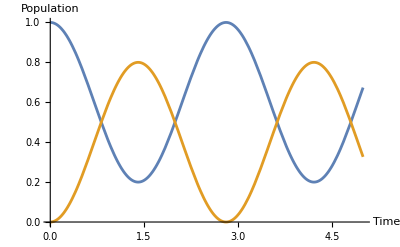

```mathematica
ρvec[t_]={{ρ00[t]},{ρ01[t]} ,{ρ10[t]},{ρ11[t]}};
s=NDSolve[{(ρvec'[t])[[1]]==-ⅈ((ρvec[t])[[3]]-(ρvec[t])[[2]]),(ρvec'[t])[[2]]==-ⅈ((ρvec[t])[[4]]-(ρvec[t])[[1]])+ⅈ(ρvec[t])[[2]], (ρvec'[t])[[3]]==-ⅈ((ρvec[t])[[1]]-(ρvec[t])[[4]])-ⅈ(ρvec[t])[[3]],(ρvec'[t])[[4]]==-ⅈ((ρvec[t])[[2]]-(ρvec[t])[[3]]), ρ00[0]==0,ρ11[0]==1,ρ01[0]==0,ρ10[0]==0}  ,{ρ00,ρ01,ρ10,ρ11},{t,0,20}];
Plot[{Evaluate[ρ11[t]/.s],Evaluate[ρ00[t]/.s]},{t,0,5},PlotRange->All,AxesLabel->{"Time","Population"}]
```